```mathematica
eqw = m x''[t] + b x'[t] + c x[t] == A Cos[ω t]
```

c x[t]+b x'[t]+m x''[t]==A Cos[t ω]

```mathematica
freq[m_,b_,c_]:=Sqrt[c/m-(b/2/m)^2]
```

```mathematica
getAmplitude[spec_]:=Module[{sol},
sol  = x[t]/.DSolve[{eqw/.spec, x[0] ==0, x'[0]==-1},x[t],t][[1]];
Return[FindMaximum[Re[sol/.t->y],{y,1000}][[1]]];
]
```

```mathematica
freq[.2, .1, .9]
```

2.10654

```mathematica
spec0={m->1,ω->2,A->1}
```

{m→1,ω→2,A→1}

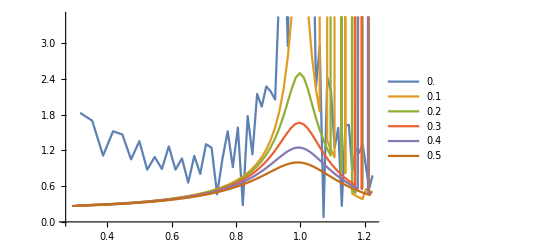

```mathematica
ListLinePlot[Table[{freq@@({m,b,c}/.Join[spec0,{c->k, b->bet}])/(ω/.spec0),
getAmplitude[Join[spec0,{c->k,b->bet}]]},{bet, .0, 0.5, 0.1},
 {k, .4, 6,.1}], PlotLegends->Range[.0,.5,.1]]
```